```mathematica
f[x_]=Piecewise[{{ⅇ^(-2*x)*Sin[x], x>0 }}]
```

Piecewise[{{ⅇ^(-2 x) Sin[x], x>0}, {0, True}}]

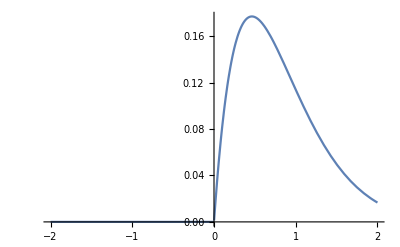

```mathematica
Plot[f[x], {x, -2,2}]
```

```mathematica
∫_(-∞)^∞ Abs[f[x]]ⅆx
```

(ⅇ^π (ⅇ^π+ⅇ^(3 π)+2 Cosh[π]))/(5 (-1+ⅇ^(2 π)) (1+ⅇ^(2 π)))

```mathematica
N[(ⅇ^π (ⅇ^π+ⅇ^(3 π)+2 Cosh[π]))/(5 (-1+ⅇ^(2 π)) (1+ⅇ^(2 π)))]
```

0.200748

```mathematica
f1[w_]:= 1/(√(2*π))∫_(-∞)^∞ f[x]*ⅇ^(-ⅈ*w*x)ⅆx
```

```mathematica
f2= 1/(√(2*π))∫_-20^20 f1[w]*ⅇ^(ⅈ*w*x)ⅆw
```

1/(8 π)ⅇ^((-2-ⅈ) x) (2 ⅈ π-2 ⅈ ⅇ^(2 ⅈ x) π-2 ⅈ ArcTan[2/21]+2 ⅈ ⅇ^(2 ⅈ x) ArcTan[2/21]-2 ⅈ ArcTan[2/19]+2 ⅈ ⅇ^(2 ⅈ x) ArcTan[2/19]+2 ⅇ^(2 ⅈ x) Gamma[0,(-2-19 ⅈ) x]+2 Gamma[0,(-2+19 ⅈ) x]-2 Gamma[0,(-2-21 ⅈ) x]-2 ⅇ^(2 ⅈ x) Gamma[0,(-2+21 ⅈ) x]+Log[89/73]-ⅇ^(2 ⅈ x) Log[73]+ⅇ^(2 ⅈ x) Log[89]+2 ⅇ^(2 ⅈ x) Log[(-2-19 ⅈ) x]+2 Log[(-2+19 ⅈ) x]-2 Log[(-2-21 ⅈ) x]-2 ⅇ^(2 ⅈ x) Log[(-2+21 ⅈ) x])

```mathematica
f22= 1/(√(2*π))∫_-10^10 f1[w]*ⅇ^(ⅈ*w*x)ⅆw
```

1/(8 π)ⅇ^((-2-ⅈ) x) (2 ⅈ π-2 ⅈ ⅇ^(2 ⅈ x) π-2 ⅈ ArcTan[2/11]+2 ⅈ ⅇ^(2 ⅈ x) ArcTan[2/11]-2 ⅈ ArcTan[2/9]+2 ⅈ ⅇ^(2 ⅈ x) ArcTan[2/9]+2 ⅇ^(2 ⅈ x) Gamma[0,(-2-9 ⅈ) x]+2 Gamma[0,(-2+9 ⅈ) x]-2 Gamma[0,(-2-11 ⅈ) x]-2 ⅇ^(2 ⅈ x) Gamma[0,(-2+11 ⅈ) x]+Log[25/17]-ⅇ^(2 ⅈ x) Log[17]+ⅇ^(2 ⅈ x) Log[25]+2 ⅇ^(2 ⅈ x) Log[(-2-9 ⅈ) x]+2 Log[(-2+9 ⅈ) x]-2 Log[(-2-11 ⅈ) x]-2 ⅇ^(2 ⅈ x) Log[(-2+11 ⅈ) x])

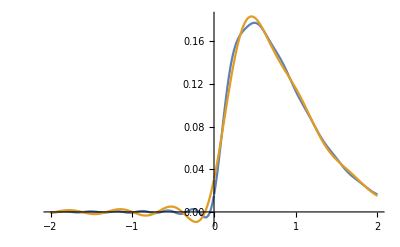

```mathematica
Plot[{Re[f2], Re[f22]}, {x, -2,2}]
```

```mathematica
g[x_]= 1/(x^2+1)
```

1/(1+x^2)

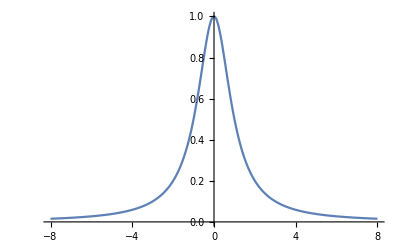

```mathematica
Plot[1/(1+x^2),{x,-8,8}]
```

```mathematica
∫_(-∞)^∞ Abs[g[x]]ⅆx
```

π

```mathematica
fb[w_]:= 1/(√(2*π))∫_(-∞)^∞ g[x]*ⅇ^(-ⅈ*w*x)ⅆx
```

```mathematica
fb1= 1/(√(2*π))∫_-20^20 fb[w]*ⅇ^(ⅈ*w*x)ⅆw
```

Integrate::idiv: Integral of ⅇ^(-ⅈ w x)/(1+x^2) does not converge on {-∞,∞}.

(ⅇ^20-Cos[20 x]+x Sin[20 x])/(ⅇ^20 (1+x^2))

```mathematica
fb2= 1/(√(2*π))∫_-10^10 fb[w]*ⅇ^(ⅈ*w*x)ⅆw
```

Integrate::idiv: Integral of ⅇ^(-ⅈ w x)/(1+x^2) does not converge on {-∞,∞}.

(ⅇ^10-Cos[10 x]+x Sin[10 x])/(ⅇ^10 (1+x^2))

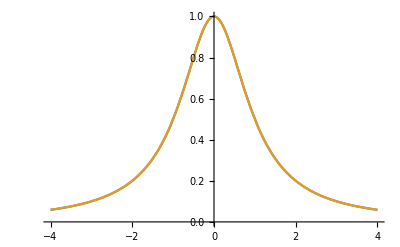

```mathematica
Plot[{Re[fb1], Re[fb2]}, {x, -4,4}]
```

```mathematica
h[a_]= a^2
```

a^2

```mathematica
∫_(-∞)^∞ Abs[h[x]]ⅆx
```

Integrate::idiv: Integral of x^2 does not converge on {-∞,∞}.

∫_(-∞)^∞ Abs[x]^2 ⅆx

```mathematica
l[x_]= Tan[x]
```

Tan[x]

```mathematica
N[∫_(-∞)^∞ Abs[l[x]]ⅆx]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {6.3887×10^56}. NIntegrate obtained 2.26713×10^243 and 2.23467×10^243 for the integral and error estimates.

2.26713×10^243

segundo punto

```mathematica
f[w_]= Piecewise[{{-w-4, -4<w<-3},{-1, -3≤w≤-2},{w+1,-2<w<-1 },{0, -1≤ w≤1},{w-1,1<w≤ 2 },{1, 2<w<3}, {-w+4,3<w<4}}]
```

Piecewise[{{-4-w, -4<w<-3}, {-1, -3≤w≤-2}, {1+w, -2<w<-1}, {0, -1≤w≤1}, {-1+w, 1<w≤2}, {1, 2<w<3}, {4-w, 3<w<4}, {0, True}}]

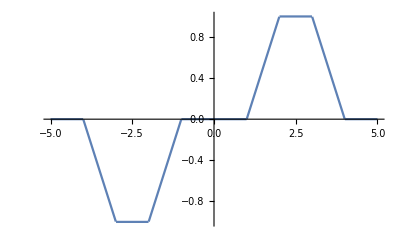

```mathematica
Plot[f[w], {w,-5,5}]
```

```mathematica
f2a = 1/(√(2*π))∫_(-∞)^∞ f[w]*ⅇ^(ⅈ*w*x)ⅆw
```

-(ⅇ^(-4 ⅈ x) (-1+ⅇ^(ⅈ x))^3 (1+2 ⅇ^(ⅈ x)+2 ⅇ^(2 ⅈ x)+2 ⅇ^(3 ⅈ x)+2 ⅇ^(4 ⅈ x)+ⅇ^(5 ⅈ x)))/(√(2 π) x^2)

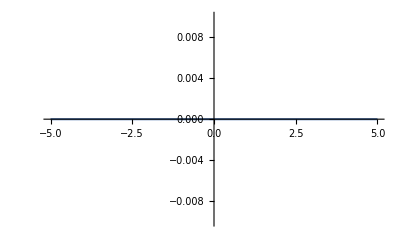

```mathematica
Plot[{Re[%100]}, {x, -5,5},PlotRange->{-0.01,0.01}]
```

```mathematica
g[w_]= Cos[4*w+π/3]
```

Sin[π/6-4 w]

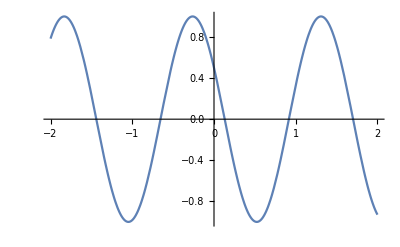

```mathematica
Plot[g[w], {w, -2,2}]
```

```mathematica
f2b = 1/(√(2*π))∫_-30^30 g[w]*ⅇ^(ⅈ*w*x)ⅆw
```

(ⅇ^(-30 ⅈ x) (4 Cos[(720+π)/6]+ⅇ^(60 ⅈ x) (ⅈ x Sin[120-π/6]-4 Sin[2/3 (-180+π)])+ⅈ x Sin[(720+π)/6]))/(√(2 π) (-16+x^2))

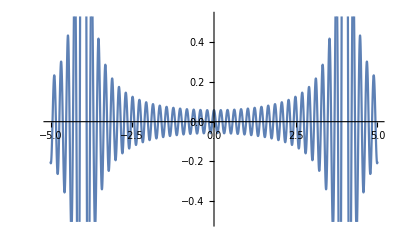

```mathematica
Plot[Re[f2b], {x, -5,5}]
```

```mathematica
l[w_]=ⅇ^(-w^2)
```

ⅇ^(-w^2)

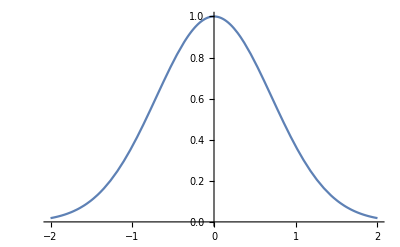

```mathematica
Plot[l[w], {w, -2,2}]
```

```mathematica
f2c = 1/(√(2*π))∫_-40^40 l[w]*ⅇ^(ⅈ*w*x)ⅆw
```

(ⅇ^(-x^2/4) (Erf[40-(ⅈ x)/2]+Erf[40+(ⅈ x)/2]))/(2 √2)

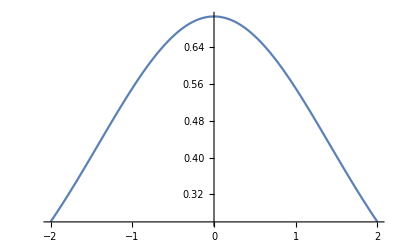

```mathematica
Plot[{Re[f2c]},{x,-2,2}]
```

```mathematica
d[w_]= w
```

w

```mathematica
f2d = 1/(√(2*π))∫_-30^30 d[w]*ⅇ^(ⅈ*w*x)ⅆw
```

(ⅈ √(2/π) (-30 x Cos[30 x]+Sin[30 x]))/x^2

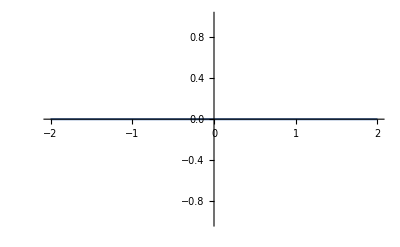

```mathematica
Plot[Re[f2d], {x, -2,2}]
```

tercer punto